```mathematica
democrats =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"-democratic-party-platform"], Length[#] > 0 &]];
```

```mathematica
demtexts =StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""], 21;;-1] & /@ democrats[[1;;31]];
```

```mathematica
demkeys = Table[StringJoin[ToString[2024 - 4*i], " Democratic Party"], {i, Range[Length[demtexts]]}];
```

```mathematica
democratTexts =Association[Table[demkeys[[i]] -> demtexts[[i]], {i, Range[Length[demtexts]]}]];
```

```mathematica
republicans =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"republican-party-platform"~~___], Length[#] > 0 &]];
```

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],21;;-1] & /@ republicans[[2;;31]];
```

```mathematica
repkeys = Table[StringJoin[ToString[2020 - 4*i], " Republican Party"], {i, Range[Length[reptexts]]}];
```

```mathematica
republicanTexts =Association[Table[repkeys[[i]] -> reptexts[[i]], {i, Range[Length[reptexts]]}]];
```

```mathematica
alltexts = Join[democratTexts, republicanTexts]
```

```mathematica
partycolors[p_] := If[StringTake[p, 6;;-1]=="Republican Party", Red, Blue]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[alltexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[alltexts], Keys[alltexts]}], ImageSize->Full, PlotRangePadding->{10, 100}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[democratTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[democratTexts], Keys[democratTexts]}], ImageSize->Full, PlotRangePadding->{10, 160}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[republicanTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[republicanTexts], Keys[republicanTexts]}], ImageSize->Full, PlotRangePadding->{10, 60}]]
```

```mathematica
republicanNominee = {"Trump","Trump","Romney","McCain","Bush","Bush","Dole","Bush","Bush","Reagan","Reagan","Ford","Nixon","Nixon","Goldwater","Nixon","Eisenhower","Eisenhower","Dewey","Dewey","Willkie","Landon","Hoover","Hoover","Coolidge","Harding","Hughes","Taft","Taft","Roosevelt","McKinley"};
```

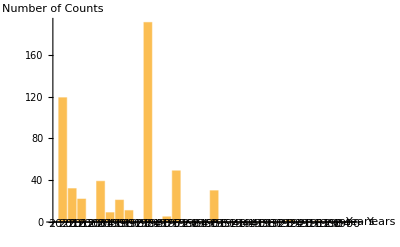

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[democratTexts], republicanNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[democratTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
democratNominee = {"Clinton", "Obama", "Obama", "Kerry", "Gore", "Clinton", "Clinton", "Dukakis", "Mondale", "Carter", "Carter", "McGovern", "Humphrey", "Johnson", "Kennedy", "Stevenson","Stevenson", "Truman", "Roosevelt", "Roosevelt", "Roosevelt", "Roosevelt", "Smith", "Davis", "Cox", "Wilson", "Wilson", "Bryan", "Parker", "Bryan"};
```

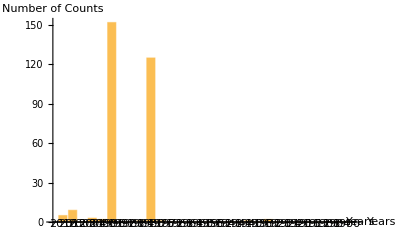

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[republicanTexts], democratNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[republicanTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
posnegtrain = ResourceData["Sample Data: Movie Review Sentence Polarity", "TrainingData"]
```

```mathematica
(*Let's think abt this*)
```

```mathematica
sentimentScore[text_,device_:"CPU"]:=With[{output=NetModel["Sentiment Language Model Trained on Amazon Product Review Data"][text,NetPort[{"LastState","Output"}],TargetDevice->device]},Switch[Depth[output],2,output[[2389]],3,output[[All,2389]]]]
```

```mathematica
testingS= TextSentences[Values[democratTexts][[1]]];
```

```mathematica
Round[Length[testingS]/4]
```

381

```mathematica
TextSeValues[democratTexts]
```

```mathematica
RandomSample[#, Round[Length[#]/4]] & /@ Table[TextSentences[p],{p, Values[democratTexts]}]
```

```mathematica
test = sentimentScore /@ RandomSample[#, Round[Length[#]/4]] & /@ Table[TextSentences[p],{p, Values[democratTexts]}];
```

$Aborted

```mathematica
test2 = sentimentScore /@ RandomSample[#, Round[Length[#]/4]] & /@ Table[TextSentences[p],{p, Values[republicanTexts]}];
```

```mathematica
test ={-0.00747268320992589,0.1854565441608429,-0.0448014922440052,0.10568365454673767,-0.004926556721329689,0.27083131670951843,0.08430567383766174,0.03317359834909439,0.05773429200053215,-0.1783575862646103,0.1104966253042221,0.11704419553279877,0.052523501217365265,-0.12432489544153214,-0.0006955271819606423,0.2342730164527893,-0.023610450327396393,-0.015193519182503223,0.009833429008722305,0.11147040873765945,0.0021419350523501635,0.0780387669801712,0.09049761295318604,0.13485389947891235,0.02547084353864193,0.03251003846526146,0.21619302034378052,0.04526978358626366,0.028890378773212433,0.06552742421627045,0.04232413321733475,0.071891650557518,0.16949772834777832,0.10027886182069778,0.058330293744802475,0.06877817958593369,-0.006463074591010809,0.08567193895578384,0.019567130133509636,0.012774437665939331,0.09798627346754074,0.06828169524669647,0.11146236211061478,-0.06734421849250793,0.28116464614868164,0.04301314800977707,-0.006501955445855856,-0.032814640551805496,-0.0843534991145134,0.17273734509944916,0.06446612626314163,0.08193248510360718,0.08728602528572083,0.14209231734275818,-0.055431779474020004,0.13144652545452118,0.1479169726371765,0.19952484965324402,-0.2421806901693344,0.066460981965065,0.031733084470033646,0.046643149107694626,0.04509027674794197,0.055279627442359924,-0.11237514764070511,0.02610533870756626,-0.028083937242627144,-0.01001521572470665,0.011227094568312168,0.06985590606927872,0.2342885285615921,0.005332335829734802,-0.11679232120513916,0.11804415285587311,0.070835180580616,0.006378243677318096,0.057053398340940475,0.012857629917562008,-0.0021276725456118584,0.007575911469757557,0.03655334189534187,0.02890995889902115,0.012080238200724125,0.04558069258928299,0.11547152698040009,0.010076689533889294,-0.003958496730774641,0.0813143253326416,0.03810612112283707,-0.02556304633617401,0.15376871824264526,0.10672028362751007,0.060308750718832016,0.08903971314430237,0.1048424020409584,0.07146614789962769,0.09322874248027802,0.03238903731107712,-0.1790609359741211,0.022683024406433105,0.02793990820646286,-0.017707930877804756,-0.09234313666820526,0.18659821152687073,0.0651811882853508,0.07808812707662582,0.12433847784996033,0.05127078667283058,0.10686181485652924,-0.019692471250891685,-0.007291014306247234,-0.06259480863809586,0.0944565013051033,-0.07781120389699936,-0.04528234526515007,0.046757470816373825,0.02564963325858116,0.15829996764659882,0.04179231822490692,0.07857659459114075,-0.0978214219212532,0.1518820971250534,0.09026612341403961,-0.18804149329662323,0.046244990080595016,0.0065308986231684685,0.27328166365623474,0.16369716823101044,-0.04081550985574722,0.09318152070045471,0.05849069729447365,0.03183726221323013,0.1055806428194046,-0.05834781005978584,-0.10280806571245193,0.20181269943714142,0.03739442676305771,0.15494270622730255,-0.11652237921953201,0.11453450471162796,-0.0006803097203373909,0.16825968027114868,0.09051553159952164,0.09268142282962799,0.018866850063204765,0.05582869425415993,0.1682041734457016,0.08615311235189438,0.03423754870891571,0.05680930241942406,0.0011835240293294191,0.027215322479605675,-0.03455528989434242,0.02889486961066723,0.0484330989420414,0.0466485396027565,-0.026897236704826355,-0.04134346917271614,0.00223307847045362,-0.004814649932086468,-0.04980066046118736,0.22671183943748474,0.1439867466688156,0.14249327778816223,0.02113177999854088,0.12156221270561218,0.059712477028369904,0.08054111152887344,-0.03642336279153824,0.004283651243895292,0.07368084788322449,-0.03241092339158058,0.0721595361828804,0.09038908034563065,0.06389802694320679,0.06534889340400696,-0.008956494741141796,0.07099651545286179,0.49539855122566223,0.10306853801012039,0.029295936226844788,-0.1564190834760666,0.12048133462667465,0.009897231124341488,0.07627639174461365,-0.04139767587184906,-0.13516636192798615,0.026711195707321167,0.1161816343665123,0.09999750554561615,0.17615345120429993,0.08628026396036148,0.02944665029644966,-0.009356760419905186,0.06528614461421967,0.04802137240767479,0.14352726936340332,0.006629280745983124,-0.013417190872132778,0.07498744875192642,0.04565979167819023,0.12957125902175903,0.03621183708310127,-0.03061620146036148,-0.02676580101251602,0.1626369059085846,0.09413520246744156,-0.12365105748176575,-0.12688535451889038,-0.03991281986236572,-0.011755629442632198,0.1369417905807495,0.0833113044500351,0.011805384419858456,0.007606593891978264,-0.08423533290624619,0.0578133799135685,-0.035751454532146454,0.08252478390932083,0.13076867163181305,-0.03585183992981911,0.014956168830394745,0.15032510459423065,0.08142831176519394,0.07868465036153793,0.16092224419116974,0.10567895323038101,-0.061064355075359344,0.10859987139701843,0.14020787179470062,-0.021893899887800217,0.0014427724527195096,0.08239493519067764,0.02633773535490036,0.06887975335121155,-0.4859047532081604,0.06709693372249603,0.019159184768795967,0.08897140622138977,0.04809579625725746,0.04267120733857155,-0.04143064096570015,0.07802460342645645,0.008605388924479485,0.29654645919799805,0.3023458421230316,0.023223640397191048,-0.01757173053920269,0.05286459997296333,0.15878741443157196,0.13837255537509918,0.2602451741695404,-0.03877327963709831,0.04949348792433739,0.14452320337295532,0.14379465579986572,-0.14359977841377258,0.10646527260541916,0.04036397486925125,0.06870977580547333,-0.03784980624914169,0.148461252450943,0.3377929627895355,0.3074357509613037,-0.06051729619503021,0.0162776168435812,-0.04870353639125824,0.05744828283786774,0.05031668394804001,0.04660069942474365,-0.06993517279624939,0.2382487803697586,0.013080238364636898,0.1184336319565773,0.3535822927951813,0.09828004240989685,0.005057701375335455,0.04024696350097656,0.10871078073978424,0.04421836510300636,-0.12866009771823883,0.07377514243125916,0.11327514052391052,0.04060668125748634,0.02041570097208023,0.10176876187324524,0.23942050337791443,0.29623398184776306,0.04255285859107971,0.1306537240743637,0.07457883656024933,-0.00022203299158718437,0.02520212158560753,0.03057653270661831,0.19922493398189545,0.08169366419315338,0.007645442150533199,0.1737012416124344,-0.19917349517345428,0.058570846915245056,0.4339643716812134,0.10000473260879517,-0.02077435702085495,0.013258041813969612,0.17724157869815826,-0.025344526395201683,0.09900559484958649,-0.056303124874830246,-0.010332067497074604,0.052549734711647034,0.20401954650878906,0.03398610278964043,-0.02805733121931553,0.03355716913938522,0.11996729671955109,0.21316339075565338,0.01774451695382595,0.09072163701057434,-0.031752925366163254,0.07101351022720337,0.061881955713033676,0.045130763202905655,0.05518903583288193,-0.10613814741373062,0.06386727094650269,0.08000163733959198,0.22163133323192596,0.044341541826725006,0.03291524946689606,-0.014091982506215572,0.46859151124954224,0.11785102635622025,0.08768095076084137,0.0193739403039217,-0.01179103460162878,-0.0015634680166840553,0.11651331186294556,0.1874147355556488,0.20991858839988708,0.050161413848400116,-0.1668563336133957,0.022839322686195374,0.07939033955335617,0.07205027341842651,0.04119480028748512,0.05373520031571388,0.03041679598391056,0.02030821703374386,0.04523952305316925,-0.0005555798416025937,-0.024720443412661552,0.03517879173159599,0.06934594362974167,0.15604239702224731,0.06234331801533699,0.2205730825662613,0.11163941770792007,0.023441758006811142,0.18346232175827026,0.1263241469860077,-0.04695132374763489,-0.026669539511203766,0.1129097044467926,-0.011690180748701096,0.1064368188381195,-0.01192647498100996,-0.09483542293310165,-0.04899173602461815,0.09771252423524857,0.17293447256088257,0.09187229722738266,0.07848866283893585,0.2041359841823578,0.04923386126756668,0.06253588944673538,0.12238120287656784,0.09066116064786911,0.1868429332971573,0.021107476204633713,0.06080712750554085,0.0931878313422203};
```

```mathematica
classing = Counts[Table[Which[-0.1 < x < 0.1, "Neutral", x < -0.1, "Negative", x > 0.1, "Positive"], {x, test}]]
```

<|Neutral→261,Positive→101,Negative→19|>

```mathematica
Mean[Table[sentimentScore[s], {s, RandomSample[TextSentences[Values[democratTexts][[1]]], 200]}]]
```

$Aborted

```mathematica
(*up to here*)
```

```mathematica
neutPart = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/political_social_media.csv", "Data", HeaderLines->1]
```

```mathematica
classNeutPart = Table[StringReplace[ToString[s[[21]]], PunctuationCharacter:>""]->s[[8]], {s, neutPart}]
```

```mathematica
indices=RandomSample[Range[Length[libcons]],Min[subsetSize,Length[libcons]]];
```

```mathematica
datasetDown=Values[Keys/@GroupBy[Thread[DimensionReduce[Keys[classlibcons],2,Method->"TSNE"]->Values[classlibcons]],Values]];
```

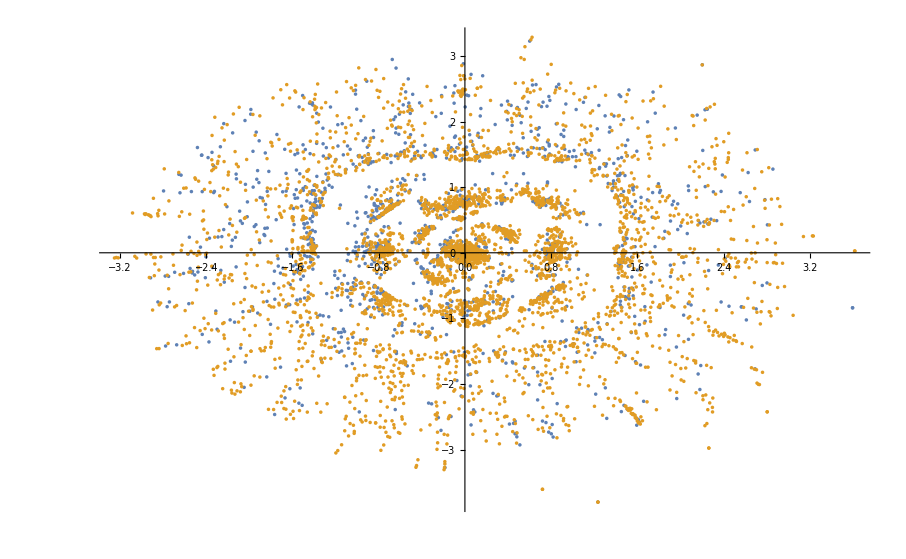

```mathematica
ListPlot[datasetDown]
```

```mathematica
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][classNeutPart];
```

```mathematica
neutPartF = Classify[classNeutPart, Method->"RandomForest"]
```

ClassifierFunction[…]

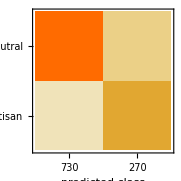
Classifier Measurements
Classifier method | Markov
Number of test examples | 1000
Accuracy | (94.30.7) %
Accuracy baseline | (76.51.3) %
Geometric mean of probabilities | 0.774 ± 0.035
Mean cross entropy | 0.256 ± 0.045
Single evaluation time | 2.47 ms/example
Batch evaluation speed | 2.94 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[neutPartF,testSet]
```

```mathematica
demPartisanCount = Mean[Table[ps["partisan"],{ps, libconsf[TextSentences[#],"Probabilities"]}]]& /@ Values[democratTexts]
```

{0.703211,0.696444,0.658335,0.654036,0.598425,0.647225,0.664165,0.598313,0.720076,0.698671,0.641517,0.710451,0.722308,0.600104,0.620425,0.671227,0.699819,0.599839,0.62437,0.557367,0.692662,0.616512,0.706971,0.734935,0.703282,0.715068,0.710106,0.786173,0.786319,0.806267,0.79256}

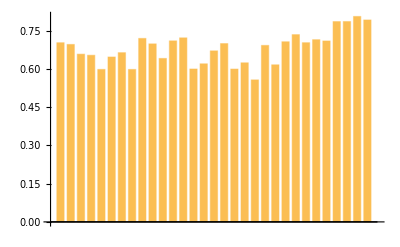

```mathematica
BarChart[demPartisanCount]
```

```mathematica
repPartisanCount = Mean[Table[ps["partisan"],{ps, libconsf[TextSentences[#],"Probabilities"]}]]& /@ Values[republicanTexts]
```

{0.708057,0.684293,0.65792,0.567213,0.663928,0.689252,0.658059,0.631696,0.63709,0.703443,0.669713,0.622125,0.622125,0.696871,0.632323,0.590069,0.717187,0.643967,0.662785,0.74188,0.675587,0.708868,0.68367,0.705545,0.782417,0.813895,0.746157,0.711108,0.741839,0.668466}

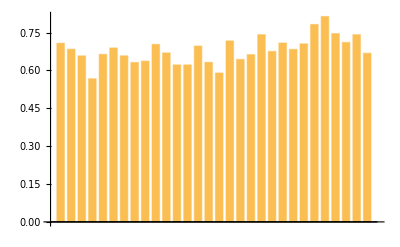

```mathematica
BarChart[repPartisanCount]
```

```mathematica
partisanCount = Counts[libconsf[TextSentences[#]]]&/@ Values[democratTexts]
```

{<|neutral→444,partisan→1081|>,<|partisan→742,neutral→307|>,<|partisan→732,neutral→352|>,<|neutral→366,partisan→744|>,<|partisan→576,neutral→364|>,<|partisan→755,neutral→378|>,<|neutral→270,partisan→563|>,<|partisan→220,neutral→144|>,<|partisan→52,neutral→19|>,<|partisan→1178,neutral→477|>,<|partisan→1056,neutral→574|>,<|neutral→236,partisan→623|>,<|partisan→662,neutral→232|>,<|neutral→257,partisan→402|>,<|partisan→538,neutral→315|>,<|partisan→540,neutral→244|>,<|partisan→384,neutral→155|>,<|neutral→143,partisan→227|>,<|partisan→104,neutral→63|>,<|neutral→35,partisan→46|>,<|neutral→52,partisan→132|>,<|neutral→34,partisan→54|>,<|partisan→31,neutral→14|>,<|partisan→152,neutral→50|>,<|partisan→162,neutral→62|>,<|partisan→139,neutral→50|>,<|partisan→96,neutral→41|>,<|partisan→99,neutral→25|>,<|partisan→84,neutral→22|>,<|partisan→68,neutral→16|>,<|partisan→60,neutral→14|>}

```mathematica
(*Bad*)
```

```mathematica
libCon = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/master_df.csv", "Data", HeaderLines->1]
```

```mathematica
removeSet = {"a","about","above","across","after","afterwards","again","against","all","almost","alone","along","already","also","although","always","am","among","amongst","amoungst","amount","amp","an","and","another","any","anyhow","anyone","anything","anyway","anywhere","are","around","as","at","back","be","became","because","become","becomes","becoming","been","before","beforehand","behind","being","below","beside","besides","between","beyond","bill","both","bottom","but","by","call","can","cannot","cant","co","com","con","could","couldnt","cry","de","describe","detail","did","do","does","done","down","due","during","each","eg","eight","either","eleven","else","elsewhere","empty","enough","etc","even","ever","every","everyone","everything","everywhere","except","few","fifteen","fifty","fill","find","fire","first","five","for","former","formerly","forty","found","four","from","front","full","further","get","give","go","had","has","hasnt","have","he","hence","her","here","hereafter","hereby","herein","hereupon","hers","herself","him","himself","his","how","however","https","hundred","i","ie","if","in","inc","indeed","interest","into","is","it","its","itself","just","keep","last","latter","latterly","least","less","like","ltd","made","many","may","me","meanwhile","might","mill","mine","more","moreover","most","mostly","move","much","must","my","myself","name","namely","neither","never","nevertheless","next","nine","no","nobody","none","noone","nor","not","nothing","now","nowhere","of","off","often","on","once","one","only","onto","or","other","others","otherwise","our","ours","ourselves","out","over","own","part","per","perhaps","please","put","rather","re","same","say","says","see","seem","seemed","seeming","seems","serious","several","she","should","show","side","since","sincere","six","sixty","so","some","somehow","someone","something","sometime","sometimes","somewhere","still","such","system","take","ten","than","that","the","their","them","themselves","then","thence","there","thereafter","thereby","therefore","therein","thereupon","these","they","thick","thin","things","third","this","those","though","three","through","throughout","thru","thus","to","together","too","top","toward","towards","twelve","twenty","two","un","under","until","up","upon","us","very","via","want","was","watch","we","well","were","what","whatever","when","whence","whenever","where","whereafter","whereas","whereby","wherein","whereupon","wherever","whether","which","while","whither","who","whoever","whole","whom","whose","why","will","with","within","without","would","www","x200b","yet","you","your","yours","yourself","yourselves"};
```

```mathematica
classLibCon = Table[StringReplace[StringJoin[Riffle[TextWords[ToString[s[[3]]]]/. Table[w->"",{w, removeSet}], " "]], PunctuationCharacter:>""]->If[s[[4]]==0, "Conservative", "Liberal"], {s, libCon}];
```

```mathematica
classLibCon = Table[StringReplace[DeleteStopwords[ToString[s[[3]]]], PunctuationCharacter:>""]->If[s[[4]]==0, "Conservative", "Liberal"], {s, libCon}];
```

```mathematica
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][classLibCon];
```

```mathematica
libConF = Classify[trainSet]
```

ClassifierFunction[…]

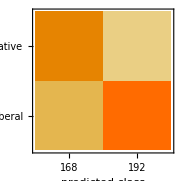
Classifier Measurements
Classifier method | Markov
Number of test examples | 360
Accuracy | (71.12.4) %
Accuracy baseline | (55.62.6) %
Geometric mean of probabilities | 0.336 ± 0.041
Mean cross entropy | 1.09 ± 0.12
Single evaluation time | 2.43 ms/example
Batch evaluation speed | 3.23 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[libConF, testSet]
```

```mathematica
libConF = Classify[classLibCon]
```

ClassifierFunction[…]

```mathematica
Counts[libConF[TextSentences[Values[democratTexts][[1]]]]]
```

<|Conservative→1429,Liberal→96|>

```mathematica
testing = Mean[Table[ps["Liberal"],{ps,libConF[TextSentences[#], "Probabilities"]}]] & /@ Values[democratTexts]
```

{0.0906621,0.134686,0.106296,0.108966,0.130673,0.0964915,0.112803,0.0777427,0.0351542,0.0935322,0.0894019,0.0916777,0.0824136,0.076665,0.0430849,0.0780739,0.0827304,0.066213,0.070371,0.0846131,0.0574465,0.0386614,0.00867073,0.0424787,0.0356201,0.0219026,0.052286,0.0139061,0.0154346,0.00471323,0.0222954}

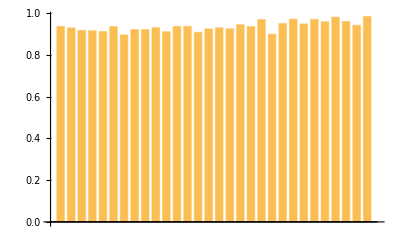

```mathematica
BarChart[testing]
```

```mathematica
(*up to here*)
```

```mathematica
Reverse[Values[alltexts]][[1]]
```

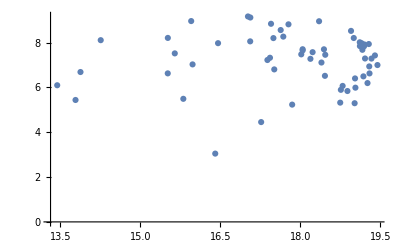

```mathematica
ListPlot[DimensionReduce[Values[alltexts], Method->"UMAP"]]
```

```mathematica
clusters = FindClusters[DimensionReduce[Values[alltexts], Method->"UMAP"], Method->"DBSCAN"];
```

```mathematica
clusters
```

{{{24.0313,0.117034},{22.8691,-0.0773432},{24.2106,3.61186},{22.7795,2.20711},{26.3253,0.514411},{21.9416,6.27227},{26.0777,4.61802},{22.3312,1.2789},{25.1926,-0.29564},{21.454,0.69794},{20.7527,0.835419},{21.819,3.36338},{25.5361,0.301236},{24.6046,5.2513}},{{20.7461,3.68589},{21.2468,4.0075}},{{19.0574,3.40789},{19.1302,3.27768},{19.9875,3.5645},{19.0743,3.68901},{19.2289,3.41366},{20.0799,3.52696},{19.1248,3.0846},{19.1266,3.32175},{18.8365,3.51083},{19.501,3.39937},{19.4075,3.41823},{19.0136,3.5336},{19.2032,3.44683},{19.1594,3.66977}},{{20.436,5.43132},{19.6665,4.66282},{19.4025,4.55531},{19.127,4.51295},{19.3841,4.43077},{20.4566,5.29338},{20.4424,5.1452},{19.9858,4.90678},{20.4017,5.28305},{19.2695,4.47331},{18.9214,4.30578},{19.7164,4.76633},{19.3146,4.51468},{19.7721,4.99391},{19.3367,4.59023},{19.7902,4.93025},{19.4513,4.51302},{19.038,4.29476},{20.4132,5.26458},{18.9646,4.21907},{19.0503,4.28116}},{{20.0587,1.90454},{20.3821,2.42631},{19.9141,2.28422},{19.8487,1.77216},{19.8381,2.04466},{19.7051,2.5501},{20.9615,2.64145},{19.4955,2.63813}},{{21.2002,2.01187},{21.0439,1.94321}}}

```mathematica
umapDRAll = DimensionReduce[Values[alltexts], Method->"UMAP"]
```

```mathematica
clusterKeys = ClusteringComponents[umapDRAll, Automatic, 1, Method->"DBSCAN"]
```

{4,4,4,5,4,4,5,4,2,2,1,5,3,5,3,3,1,1,2,3,3,3,2,2,3,3,3,3,2,3,3,5,5,5,5,5,4,5,4,1,2,5,1,2,3,2,1,2,3,2,2,2,3,3,3,3,3,3,3,3,2}

```mathematica
Table[Table[Callout[#, ]]]
```

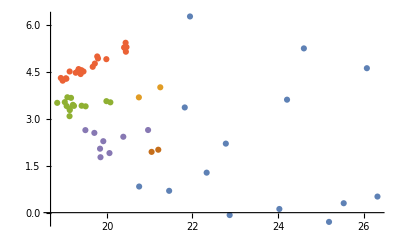

```mathematica
ListPlot[clusters]
```

```mathematica
ClusteringComponents[DimensionReduce[Values[democratTexts], Method->"UMAP"], Automatic, 1, Method->"DBSCAN"]
```

{11,1,1,1,3,5,6,1,1,1,10,7,3,9,1,1,1,4,1,1,1,1,1,1,2,2,8,2,1,1,1}

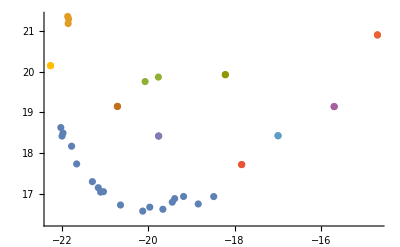

```mathematica
ListPlot[FindClusters[DimensionReduce[Values[democratTexts], Method->"UMAP"], Method->"DBSCAN"]]
```

```mathematica
Length[FindClusters[DimensionReduce[RandomSample[TextSentences[Values[democratTexts][[1]]], 50], Method->"UMAP"], Method->"DBSCAN"]]
```

3

```mathematica
FeatureExtract[TextWords/@{"Jupiter is the largest planet","Mars is the fourth planet from the sun"},"TFIDF"]//MatrixForm
```

(0.135911 | 0. | 0. | 0. | 0.135911 | 0. | 0. | 0. | 0.
0. | 0.0855737 | 0.0855737 | 0. | 0. | 0.0855737 | 0.0855737 | 0. | 0.)